```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_BITW70/";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{6.45996,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.020432,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW70 Price | % Change | log return future | log return BITW70
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 66494.6 | 3.56% | 0.0212907 | 0.0349856
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 64208.5 | -27.64% | -0.0904653 | -0.323453
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 88729.2 | 3.52% | -0.0196938 | 0.0345513
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 85715.8 | -0.35% | -0.131645 | -0.109017
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 95588.7 | 8.73% | 0.03685 | 0.0836779
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 87915.6 | -10.53% | -0.119603 | -0.111227
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 98258.7 | -1.26% | -0.042369 | -0.0126896
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 99513.6 | 6.52% | 0.018947 | 0.0631607
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 93422.6 | -6.54% | -0.0359909 | -0.110025)

```mathematica
data[[1,8]]
```

log return BITW70

```mathematica
data[[1,7]]
```

log return future

```mathematica
tmp=Import[NotebookDirectory[] <> "data_bitw70/" <> ToString[kk] <> "_parameters.csv"]
```

(2021-05-20
1.46872
-0.953974
0.456849)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,8]]];
v=hatF[data[[2;;,7]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_bitw70/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.160197 | 0.0812984
0.00427991 | 0.00369993
0.697186 | 0.51833
0.741325 | 0.49263
0.951261 | 0.928881
0.748265 | 0.97804
0.726705 | 0.448171
0.854463 | 0.662627
0.427871 | 0.572509
0.99476 | 0.9986)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.100435,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{1.96138,1.47453,0.358376,3.41058,1.79762}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{1.86241,2.88395,0.397049,3.1236,1.79405}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.573683,0.00246259,0.187131,0.00707186,0.799013}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.572112,0.0072471,0.186992,0.00803653,0.795492}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

82.5767

```mathematica
%/Length[data]
```

0.274341

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

{18.9954,95.8528}

```mathematica
%/Length[data]
```

{0.0631076,0.318448}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=80, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,8]]];
v=hatF[data[[2;;,7]]];
tmp=Import[NotebookDirectory[] <> "data_bitw70/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-6.6427}. NIntegrate obtained 0.00175968 and 1.80961×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-6.1119}. NIntegrate obtained 0.00209767 and 2.31549×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-6.31512}. NIntegrate obtained 0.00191426 and 1.01961×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tLL
```

{95.8528,114.739,109.814,114.844,111.782,112.672,112.827,116.864,107.756,107.132,102.614,106.47,95.827,106.572,100.954,101.562,110.669,113.655,117.591,111.903,115.666,124.533,124.884,117.426,124.595,116.132,114.449,122.394,124.442,129.693,122.007,116.164,117.065,113.997,132.905,128.843,137.975,125.996,125.943,126.677,126.845,133.701,145.861,140.338,138.178,135.836,134.356,131.438,138.904,137.3,138.38,137.35,138.958,137.633,127.32,129.259,134.91,134.619,131.273,131.119,132.152,123.231,135.513,131.256,130.354,136.205,140.933,153.753,144.688,146.52,145.264,138.676,138.599,141.192,142.943,143.251,138.073,148.671,148.902,145.442,138.832}

```mathematica
mLL
```

{0.318448,0.381191,0.36483,0.38154,0.371368,0.374327,0.374839,0.388252,0.357994,0.35592,0.34091,0.353721,0.318362,0.354059,0.335397,0.337416,0.367671,0.37759,0.390669,0.371772,0.384271,0.41373,0.414897,0.39012,0.413936,0.385821,0.380229,0.406624,0.413429,0.430873,0.405339,0.385927,0.38892,0.378727,0.441544,0.428051,0.458387,0.41859,0.418417,0.420853,0.42141,0.444188,0.484588,0.466239,0.459065,0.451283,0.446366,0.436673,0.461475,0.456145,0.459733,0.456312,0.461656,0.457251,0.422989,0.429432,0.448206,0.447238,0.436124,0.43561,0.439044,0.409405,0.450209,0.436067,0.43307,0.452509,0.468216,0.510807,0.480692,0.486778,0.482604,0.460719,0.460461,0.469077,0.474895,0.475917,0.458714,0.493922,0.494693,0.483196,0.461236}

```mathematica
Export[NotebookDirectory[] <> "data_bitw70/LL_NIG_bitw70.csv", Prepend[{Range[0,80],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data_bitw70/LL_NIG_bitw70.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

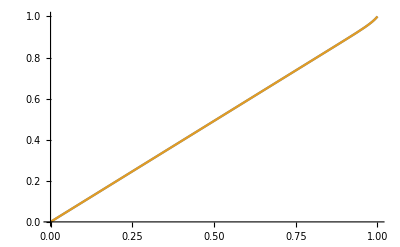

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

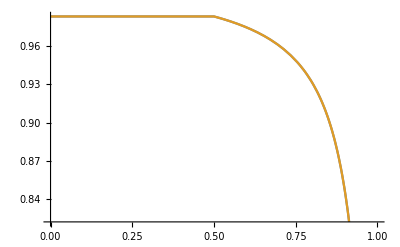

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

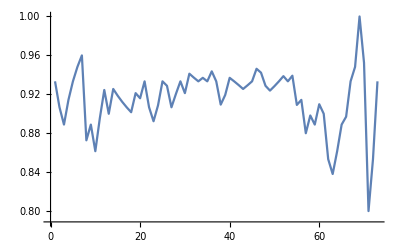

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

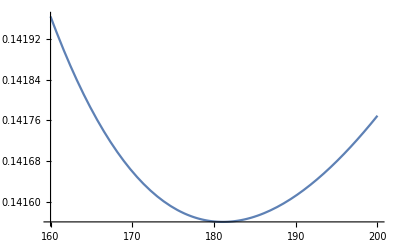

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```